```mathematica
ClearAll["Global`*"]
```

Define colors for graphs

```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
```

## System Description

The system consists of two individual thermal transistors S1 and S2, connected in a Darlington pair configuration. 
S1 - Connected to three thermal baths, B_HOT (collector), B_CNT (base) and B_INT (emitter)
S2 - Connected to three thermal baths, B_HOT (collector), B_INT (base) and B_COL (emitter)

The thermal bath B_HOT is at a high temperature, while B_COL is at a low temperature. The temperature T_CNT of control terminal  B_CNT can be varied.
The temperature T_INT of the intermediate bath B_INT is not controllable, but is determined by the thermal equilibrium condition.

In this context, the thermal equilibrium condition would be that heat inflow to the bath B_INT from S1 should match the heat outflow to S2 from bath B_INT.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper. However, we use a simplified 4×4 density matrix model instead of the previous 8×8 model. This is only valid under the conditions
	1. ω_L=ω_M=ω_R = 0
	2. ω_RL=0

## Deriving the quantum master equation for a single transistor or a single optical gate

The simplified model for the individual transistors are taken from “Simplified Optically Controlled Thermal Gate - Resonant Optical Drive”.

The index S represents which transistor is considered.

Eigenstates,
|1> = |+z,+z,+z> = |-z,-z,-z>
|2> = |+z,+z,-z> = |-z,-z,+z>
|3> =|+z,-z,+z> = |-z,+z,-z> 
|4> =|+z,-z,-z> = |-z,+z,+z>

### Density matrix

```mathematica
Subscript[ρMatrix, S_][t_]:=Table[Subscript[ρ, S,i,j][t],{i,1,4},{j,1,4}];
MatrixForm[Subscript[ρMatrix, 1][t]]
```

(ρ_(1,1,1)[t] | ρ_(1,1,2)[t] | ρ_(1,1,3)[t] | ρ_(1,1,4)[t]
ρ_(1,2,1)[t] | ρ_(1,2,2)[t] | ρ_(1,2,3)[t] | ρ_(1,2,4)[t]
ρ_(1,3,1)[t] | ρ_(1,3,2)[t] | ρ_(1,3,3)[t] | ρ_(1,3,4)[t]
ρ_(1,4,1)[t] | ρ_(1,4,2)[t] | ρ_(1,4,3)[t] | ρ_(1,4,4)[t])

### System Hamiltonian

```mathematica
Subscript[HsMatrix, S_]:=({{1/2 ℏ (Subscript[ωLM, S]+Subscript[ωMR, S]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, S]-Subscript[ωMR, S]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, S]+Subscript[ωMR, S]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, S]+Subscript[ωMR, S])}})
```

```mathematica
Subscript[HsEVal, S_][i_]:=(Eigenvalues[Subscript[HsMatrix, S]][[{4,2,1,3}]])[[i]]
Subscript[HsEVec, S_][i_]:=(Eigenvectors[Subscript[HsMatrix, S]][[{4,2,1,3}]])[[i]]
```

```mathematica
Table[Subscript[HsEVec, S][i],{i,1,4}]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Relation between eigenvalues and ωs

```mathematica
ωassum=Flatten[{Table[Subscript[ω, S,i,j]->(Subscript[HsEVal, S][i]-Subscript[HsEVal, S][j] )/ℏ,{S,1,2},{i,1,4},{j,1,4}]}];
```

### Interaction Hamiltonian with the classically modelled optical field

Ω_P represents the strength of the interaction between the device P and the optical field

```mathematica
Subscript[HlMatrix, S_]:= ({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, S])/2}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, S])/2, 0, 0}});
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S]/2 ⅈ(Subscript[ρ, S,i,j][t]-Subscript[ρ, S,j,i][t])
```

### Lindblad terms from environment interactions

Following the procedure outlined in “Optically Controlled Quantum Thermal Gate”

```mathematica
Subscript[AMatrix, S_,P_][i_]:=({{({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})}})[[P,i]]
Subscript[ωDis, S_,P_][i_]:=({{Subscript[ω, S,4,1], Subscript[ω, S,3,2]}, {Subscript[ω, S,3,1], Subscript[ω, S,4,2]}, {Subscript[ω, S,2,1], Subscript[ω, S,4,3]}})[[P,i]]
```

The dissipation terms can now be written

```mathematica
Subscript[LinMatrix, S_,P_][ρ_]:=Subscript[LinMatrix, S,P][ρ]=∑_(i=1)^2 (Subscript[J, S,P][Subscript[ωDis, S,P][i]](1+Subscript[NBE, S,P][Subscript[ωDis, S,P][i]])(Subscript[AMatrix, S,P][i].ρ.Subscript[AMatrix, S,P][i]†-1/2(Subscript[AMatrix, S,P][i]†.Subscript[AMatrix, S,P][i].ρ+ρ.Subscript[AMatrix, S,P][i]†.Subscript[AMatrix, S,P][i]))+Subscript[J, S,P][Subscript[ωDis, S,P][i]]Subscript[NBE, S,P][Subscript[ωDis, S,P][i]](Subscript[AMatrix, S,P][i]†.ρ.Subscript[AMatrix, S,P][i]-1/2(Subscript[AMatrix, S,P][i].Subscript[AMatrix, S,P][i]†.ρ+ρ.Subscript[AMatrix, S,P][i].Subscript[AMatrix, S,P][i]†)))
```

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, S_,P_][i_,j_]:=Subscript[J, S,P][Subscript[ω, S,i,j]]((1+Subscript[NBE, S,P][Subscript[ω, S,i,j]])Subscript[ρ, S,i,i][t]-Subscript[NBE, S,P][Subscript[ω, S,i,j]]Subscript[ρ, S,j,j][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, S,1][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, S,2][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, S,3][Subscript[ρMatrix, S][t]],
Flatten[Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}]]
];
MatrixForm[%]
```

(Τ_(S,1)[4,1] | 1/2 (-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,2)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,1,3)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,3)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t]-2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t])
1/2 (-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,1)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,1)[t]) | Τ_(S,1)[3,2] | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]-2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,2,4)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,4)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,4)[t])
1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,1)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,1)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]-2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]) | -Τ_(S,1)[3,2] | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,4,1)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,4)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,4)[t])
1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]-2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,1)[ω_(S,4,1)] ρ_(S,4,2)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,2)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,1)[ω_(S,3,2)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,4,1)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,3)[t]-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,3)[t]) | -Τ_(S,1)[4,1])

(Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,4)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t]) | Τ_(S,2)[4,2] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t])
1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t]) | -Τ_(S,2)[3,1] | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,4)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,4)[t])
1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,3)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,3)[t]) | -Τ_(S,2)[4,2])

(Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,4)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]) | -Τ_(S,3)[2,1] | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,4)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,4)[t])
1/2 (-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t]) | Τ_(S,3)[4,3] | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t])
1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,1)[t]) | 1/2 (-J_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,2)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,2)[t]) | 1/2 (-J_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]) | -Τ_(S,3)[4,3])

### Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, S_,P_][ω_]->Subscript[κ, S,P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
Subscript[RHSfield, S_]:=-ⅈ/ℏ(Subscript[HlMatrix, S].Subscript[ρMatrix, S][t]-Subscript[ρMatrix, S][t].Subscript[HlMatrix, S]);

Subscript[RHS, S_]:=Subscript[RHSfield, S]+Subscript[LinMatrix, S,1][Subscript[ρMatrix, S][t]]+Subscript[LinMatrix, S,2][Subscript[ρMatrix, S][t]]+Subscript[LinMatrix, S,3][Subscript[ρMatrix, S][t]];

MatrixForm[Subscript[RHS, S]]
```

(-J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,1)[t]-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]+J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t]+J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t]+J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,1,2)[t]-1/2 ⅈ Ω_S ρ_(S,1,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,1,3)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t] | -1/2 ⅈ Ω_S ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,1,4)[t]
-1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,1)[t]+1/2 ⅈ Ω_S ρ_(S,4,1)[t] | J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]-J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,2)[t]-J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]-J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t]+J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,3)[t]-(ⅈ (1/2 ℏ Ω_S ρ_(S,2,4)[t]-1/2 ℏ Ω_S ρ_(S,4,2)[t]))/ℏ+J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t]+1/2 ⅈ Ω_S ρ_(S,4,3)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,2,4)[t]-(ⅈ (1/2 ℏ Ω_S ρ_(S,2,2)[t]-1/2 ℏ Ω_S ρ_(S,4,4)[t]))/ℏ
-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t]-1/2 ⅈ Ω_S ρ_(S,3,4)[t] | J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]+J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,2,2)[t]-J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,3)[t]-J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t]-J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]+J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 ⅈ Ω_S ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,3,4)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,3,4)[t]
1/2 ⅈ Ω_S ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,4,1)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,1)[t] | -1/2 J_(S,1)[ω_(S,3,2)] NBE_(S,1)[ω_(S,3,2)] ρ_(S,4,2)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,2)[t]-(ⅈ (-1/2 ℏ Ω_S ρ_(S,2,2)[t]+1/2 ℏ Ω_S ρ_(S,4,4)[t]))/ℏ | 1/2 ⅈ Ω_S ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,3,2)] (1+NBE_(S,1)[ω_(S,3,2)]) ρ_(S,4,3)[t]-1/2 J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,3)[t] | J_(S,1)[ω_(S,4,1)] NBE_(S,1)[ω_(S,4,1)] ρ_(S,1,1)[t]+J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]+J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]-(ⅈ (-1/2 ℏ Ω_S ρ_(S,2,4)[t]+1/2 ℏ Ω_S ρ_(S,4,2)[t]))/ℏ-J_(S,1)[ω_(S,4,1)] (1+NBE_(S,1)[ω_(S,4,1)]) ρ_(S,4,4)[t]-J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t]-J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t])

```mathematica
Subscript[LHS, S_]:=D[Subscript[ρMatrix, S][t], t];

MatrixForm[Subscript[LHS, S]]
```

(ρ_(S,1,1)'[t] | ρ_(S,1,2)'[t] | ρ_(S,1,3)'[t] | ρ_(S,1,4)'[t]
ρ_(S,2,1)'[t] | ρ_(S,2,2)'[t] | ρ_(S,2,3)'[t] | ρ_(S,2,4)'[t]
ρ_(S,3,1)'[t] | ρ_(S,3,2)'[t] | ρ_(S,3,3)'[t] | ρ_(S,3,4)'[t]
ρ_(S,4,1)'[t] | ρ_(S,4,2)'[t] | ρ_(S,4,3)'[t] | ρ_(S,4,4)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
Subscript[motioneq, S_]:=Flatten[Solve[Subscript[LHS, S]==Subscript[RHS, S],Flatten[Table[Subscript[ρ, S,i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal]
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[motioneqdiag, S_]:=Subscript[motioneq, S][[1;; ;;5]];
Subscript[motioneqoffdiag, S_]:=Delete[Subscript[motioneq, S],Table[{1+5i},{i,0,3}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
Subscript[motioneqdiagtran, S_]:=
ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]&,Subscript[motioneqdiag, S]]
```

### Equations of motion for the individual transistors

Actual equations for population densities (i.e. diagonal elements of the density matrix),

```mathematica
Subscript[motioneqdiag, S];
```

Simplified version of the same equations,

```mathematica
Subscript[motioneqdiagtran, S]
```

{ρ_(S,1,1)'[t]==Τ_(S,1)[4,1]+Τ_(S,2)[3,1]+Τ_(S,3)[2,1],ρ_(S,2,2)'[t]==-Υ_S[2,4]+Τ_(S,1)[3,2]+Τ_(S,2)[4,2]-Τ_(S,3)[2,1],ρ_(S,3,3)'[t]==-Τ_(S,1)[3,2]-Τ_(S,2)[3,1]+Τ_(S,3)[4,3],ρ_(S,4,4)'[t]==Υ_S[2,4]-Τ_(S,1)[4,1]-Τ_(S,2)[4,2]-Τ_(S,3)[4,3]}

### Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, S_,P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, S,P]))-1);
```

Calculate heat current inflow, from the thermal bath into the transistor

```mathematica
Subscript[HsMatrixSimp, S_]:=DiagonalMatrix[ℏ{Subscript[ω, S,1],Subscript[ω, S,2],Subscript[ω, S,3],Subscript[ω, S,4]}];
ωassum1={Table[Subscript[ω, S,i]-> Subscript[HsMatrix, S][[i,i]]/ℏ,{S,1,2},{i,1,4}]};
```

```mathematica
Subscript[EngyFlowIn, S_,P_]:=Tr[Subscript[LinMatrix, S,P][Subscript[ρMatrix, S][t]].Subscript[HsMatrixSimp, S]]
Subscript[EngyFlowInField, S_]:=Tr[Subscript[RHSfield, S].Subscript[HsMatrixSimp, S]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, S,1],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, S,2],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, S,3],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInField, S],
Flatten[{Table[Subscript[Τs, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υs, S][i,j],{i,1,4},{j,i+1,4}]}],
Flatten[{Table[Subscript[Τ, S,P][i,j],{P,1,3},{i,1,4},{j,1,4}],Table[Subscript[Υ, S][i,j],{i,1,4},{j,i+1,4}]}]
];
Simplify[%]
```

(ℏ ω_(S,2)-ℏ ω_(S,3)) Τ_(S,1)[3,2]+(ℏ ω_(S,1)-ℏ ω_(S,4)) Τ_(S,1)[4,1]

(ℏ ω_(S,1)-ℏ ω_(S,3)) Τ_(S,2)[3,1]+(ℏ ω_(S,2)-ℏ ω_(S,4)) Τ_(S,2)[4,2]

(ℏ ω_(S,1)-ℏ ω_(S,2)) Τ_(S,3)[2,1]+(ℏ ω_(S,3)-ℏ ω_(S,4)) Τ_(S,3)[4,3]

-ℏ (ω_(S,2)-ω_(S,4)) Υ_S[2,4]

## Modeling Darlington pair system

### Modelling the interconnections of the thermal transistors

Set the terminal temperatures for each transistor

```mathematica
Tassum={
Subscript[T, 1,1]->Thot,Subscript[T, 1,2]-> Tcnt,Subscript[T, 1,3]-> Tint[t],Subscript[T, 2,1]->Thot,Subscript[T, 2,2]->Tint[t],Subscript[T, 2,3]->Tcol,
Subscript[κ, 1,1]->κhot,Subscript[κ, 1,2]->κcnt,Subscript[κ, 1,3]->κint, Subscript[κ, 2,1]->κhot,Subscript[κ, 2,2]->κint,Subscript[κ, 2,3]->κcol
};
```

Here T_HOT is fixed at a high temperature and T_COL is fixed at a low temperature. T_CNT is adjusted to get the necessary heat flow through the transistors. T_INT is determined by the internal dynamics.

### Modelling the time varying temperature T_INT[t] of the intermediate bath B_int

The internal energy of the thermal bath is an increasing function of its temperature. However, the actual relationship need not be linear.
We assume linearity of the internal energy - temperature relationship in the region we are considering.
This is similar to the heat capacity characterization we routinely use in classical physics, ΔE=mCΔT.

```mathematica
motioneqintbath=mCint D[Tint[t], t]==-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]);
```

Here mC denotes the heat capacity of the thermal bath.

## On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

### Darlington pair system

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
sysassum={
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8ωconv,
Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2ωconv,
Subscript[Ω, 1]->0.007ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02Tconv,Tcnt-> 0.02 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.01,κint->0.01,
mCint->20mCconv
};
```

```mathematica
sysassum={
Subscript[ωLM, 1]->0.3 ωconv,Subscript[ωMR, 1]->0.4ωconv,
Subscript[ωLM, 2]->0.9ωconv,Subscript[ωMR, 2]->1.1ωconv,
Subscript[Ω, 1]->0.001ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02Tconv,Tcnt-> 0.02 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.0,κint->0.01,
mCint->20mCconv
};
```

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the third are zero (ground/lowest energy state).

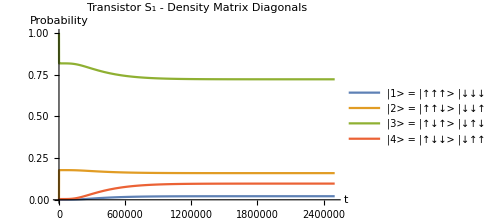
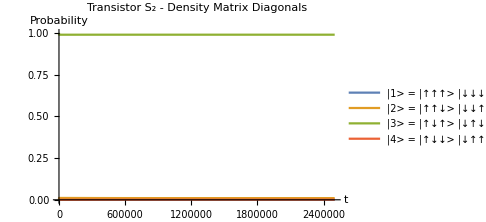

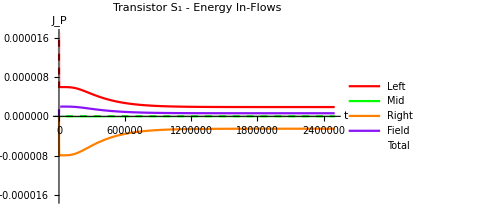
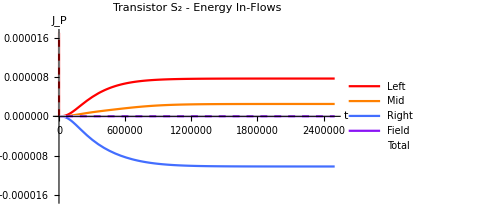

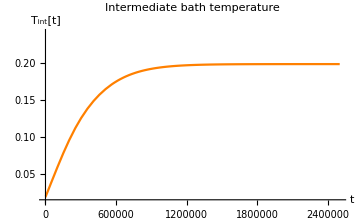

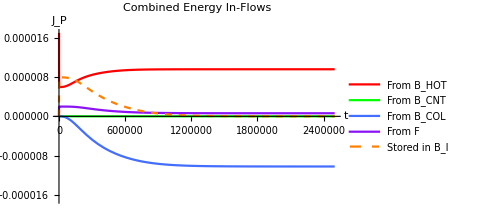

```mathematica
tmax=(10000/(Subscript[ωMR, 1] κhot))//.Flatten[{unitassum,sysassum}];

motioneqs=Simplify[{Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]];
initconditions={Tint[0]==Tcol,Table[Subscript[ρ, S,i,j][0]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,0,tmax}
];

plot1=Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,4}]}/.dynamics];
plot2=Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,4}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> |↓↓↓>"],Style["|2> = |↑↑↓> |↓↓↑>"],Style["|3> = |↑↓↑> |↓↑↓>"],Style["|4> = |↑↓↓> |↓↑↑>"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> |↓↓↓>"],Style["|2> = |↑↑↓> |↓↓↑>"],Style["|3> = |↑↓↑> |↓↑↓>"],Style["|4> = |↑↓↓> |↓↑↑>"]}]}

plot1=Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
plot2=Flatten[{
Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 2,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 2],Subscript[EngyFlowIn, 2,1]+Subscript[EngyFlowIn, 2,2]+Subscript[EngyFlowIn, 2,3]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S_1 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,Orange,PurpleC,{White,Dashed}}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S_2 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Orange,BlueC,PurpleC,{White,Dashed}}]}

Tint[t]/.dynamics;
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t"],Style["T_int[t]"]},
	PlotStyle->{Orange}
]

Flatten[{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2])
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Combined Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"From B_HOT","From B_CNT","From B_COL","From F","Stored in B_I"},
	PlotStyle->{Red,Green,BlueC,PurpleC,{Orange,Dashed}}]
```

### Single transistor system, for comparison

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
indsysassum={
Subscript[T, 1,1]-> 0.2 Tconv,Subscript[T, 1,2]-> 0.02 Tconv,Subscript[T, 1,3]-> 0.02 Tconv,
Subscript[κ, 1,1]-> 0.01,Subscript[κ, 1,2]->0.01,Subscript[κ, 1,3]-> 0.01,
Subscript[ωLM, 1]-> 0.8ωconv,Subscript[ωMR, 1]->1.2 ωconv,
Subscript[Ω, 1]->0.007 ωconv
};
```

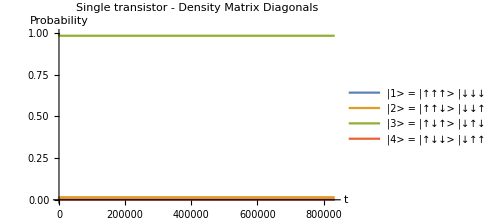

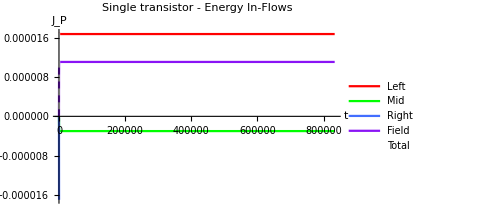

```mathematica
tmax=(10000/(Subscript[ωMR, 1] Subscript[κ, 1,1]))//.Flatten[{unitassum,indsysassum}];

motioneqs=Simplify[Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum}]];
initconditions={Table[Subscript[ρ, 1,i,j][0]==i,j i,3 1,{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,4}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> |↓↓↓>"],Style["|2> = |↑↑↓> |↓↓↑>"],Style["|3> = |↑↓↑> |↓↑↓>"],Style["|4> = |↑↓↓> |↓↑↑>"]}]

Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Single transistor - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv Subscript[κ, 1,1]/.indsysassum,1.7 10^-3 Econv Subscript[κ, 1,1]/.indsysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,BlueC,PurpleC,{White,Dashed}}]
```

## Density matrix, transition rate and energy flow at equilibrium

### Simulation of individual components at steady state

Function for density matrix elements, transition rates and energy flows,

```mathematica
Subscript[varFunc, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLMs_,ωMRs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->0,Subscript[ωM, S]->0,Subscript[ωR, S]->0,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->0}];
temp1=N[Subscript[motioneq, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^4 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,4},{j,1,4}]]]]];
Re[{Flatten[
Table[Subscript[ρ, S,i,i],{i,1,4}]/.temp3],
Flatten[{
Subscript[Τs, S,1][4,1],Subscript[Τs, S,1][3,2],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],
Subscript[Υs, S][4,2]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]}]
]
```

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.003],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.27Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[S_,ωLMs_,ωMRs_,title_,colors_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},
temp0=Flatten[{Jassum,NBEassum,k->1,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs}];label={"|1_SIMP>=|↑↑↑> |↓↓↓>","|2_SIMP>=|↑↑↓> |↓↓↑>","|3_SIMP>=|↑↓↑> |↓↑↓>","|4_SIMP>=|↑↓↓> |↓↑↑>"};posx={0,-0.5,0,0.5};posy=Diagonal[Subscript[HsMatrix, S]/(ℏ ωconv)/.Flatten[{Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs}]];nodes=var[[1]];rates=({{0, -var[[2]][[5]], -var[[2]][[3]], -var[[2]][[1]]}, {0, 0, -var[[2]][[2]], -var[[2]][[4]]}, {0, 0, 0, -var[[2]][[6]]}, {0, 0, 0, 0}});
ratesF=({{0, 0, 0, 0}, {0, 0, 0, -var[[2]][[7]]}, {0, 0, 0, 0}, {0, 0, 0, 0}});ratecolors=({{0, colors[[3]], colors[[2]], colors[[1]]}, {0, 0, colors[[1]], colors[[2]]}, {0, 0, 0, colors[[3]]}, {0, 0, 0, 0}});
ratecolorsF=({{0, 0, 0, 0}, {0, 0, 0, colors[[4]]}, {0, 0, 0, 0}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Simulation for SI units

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.100/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
```

Simulation for natural units

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
```

#### Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues of individual transistors, assuming T_INT is artificially fixed

For both temperature-controlled and optically-controlled Darlington pairs,

```mathematica
Manipulate[Module[{tempS1,tempS2},
tempS1=Subscript[varFunc, 1][Thot,Tcnt,Tint,κhot,κcnt,κint,ωLM1,ωMR1,Ω1,unitassum];
tempS2=Subscript[varFunc, 2][Thot,Tint,Tcol,κhot,κint,κcol,ωLM2,ωMR2,Ω2,unitassum];
{
DrawFunc[1,ωLM1,ωMR1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,tempS1],
DrawFunc[2,ωLM2,ωMR2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,tempS2],
BarChart[tempS1[[3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[tempS2[[3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}],
BarChart[{ -tempS1[[3,3]],-tempS2[[3,2]],-tempS1[[3,3]]-tempS2[[3,2]]}
,ChartLabels->{"S_1 - Right","S_2 - Mid","Total inflow"},PlotLabel->"Energy inflows to intermediate bath",AxesLabel->{"","J_P"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,White}]
}
],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.08 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Intermediate Bath Temperature",Alignment->Center],
{{Tint,0.14 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωLM1,0.9ωconv},0ωconv,2ωconv},
{{ωMR1,1.1ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv}]
```

### Simulation of combined system at steady state

#### Finding the stable solution for a given configuration

Simulation for natural units. Required because FindRoot algorithm seems to get a lot of numerical errors when very small numbers are used

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
```

```mathematica
sysassum1:={
Subscript[ωLM, 1]->0.9 ωconv,Subscript[ωMR, 1]->1.1 ωconv,
Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1ωconv,
Subscript[Ω, 1]->0.0ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02 Tconv,Tcnt-> 0.04 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.01,κint->0.01
};
```

Conditions for the steady state solutions. The time derivatives have all become zero.

```mathematica
statassum=Flatten[{
Tint'[t]->0,
Tint[t]->Tint,
Table[Subscript[ρ, S,i,j]'[t]->0,{S,1,2},{i,1,4},{j,1,4}],
Table[Subscript[ρ, S,i,j][t]->Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}]
}];
```

Conditions for the density matrices to be valid.

```mathematica
Subscript[denmateq, S_]:=∑_(i=1)^4 Subscript[ρ, S,i,i]==1
```

The equations of motion consists of
	2×12 off diagonal equations, 
	2×3 diagonal equations (one is removed since not all 8 equations are independent of each other), 
	2 density matrix trace equations, 
	1 equation for the intermediate bath

```mathematica
stateqns=Expand[Flatten[{
Subscript[motioneqoffdiag, 1],Subscript[motioneqoffdiag, 2],
Subscript[motioneqdiag, 1][[1;;3]],Subscript[motioneqdiag, 2][[1;;3]],
Subscript[denmateq, 1],Subscript[denmateq, 2],
motioneqintbath}]];
```

Generate a random point starting point for the equation solver

```mathematica
startpoints:=Module[{temp},
temp=Flatten[Table[{Subscript[ρ, S,i,j],RandomReal[{0,1}]},{S,1,2},{i,1,4},{j,1,4}],2];
AppendTo[temp,{Tint,RandomReal[{Tcol/.sysassum1,Thot/.sysassum1}]}]
];
```

Run the solver. “Solve” doesn’t work since this is a complicated non-linear equation

```mathematica
statsol=FindRoot[stateqns//.Flatten[{statassum,unitassum,ωassum,ωassum1,sysassum1,Jassum,NBEassum,Tassum}],startpoints];
Tint/.statsol
```

0.0610811+0. ⅈ

#### Combining above methodology into a single function

```mathematica
combinedVarFunc[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κints_,κcols_,ωLM1_,ωMR1_,Ω1_,ωLM2_,ωMR2_,Ω2_,unitassum_]:=
Module[{temp0,temp1,temp2},
temp0=Flatten[{statassum,unitassum,Jassum,NBEassum,ωassum,ωassum1,Tassum,
Thot->Thots,Tcnt->Tcnts,Tcol->Tcols,
κhot->κhots,κcnt->κcnts,κint->κints,κcol->κcols,
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[Ω, 1]->Ω1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,Subscript[Ω, 2]->Ω2}];

temp1=stateqns//.temp0;
temp2=FindRoot[temp1,startpoints];
Re[{Tint//.temp2,Table[{
	Table[Subscript[ρ, S,i,i],{i,1,4}]/.temp2,
	{
		Subscript[Τs, S,1][4,1],Subscript[Τs, S,1][3,2],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],
Subscript[Υs, S][4,2]
	}//.Flatten[{temp0,temp2}],
	{
		Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
	}//.Flatten[{temp0,temp2}]
},{S,1,2}]
}]
]
```

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2},
ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω1=0.003ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,unitassum]
]
```

{0.162376,{{{6.5387×10^-6,0.0108163,0.987929,0.00124804},{6.66726×10^-8,1.44312×10^-6,-1.30774×10^-7,2.49521×10^-6,6.41015×10^-8,1.31234×10^-6,-3.87423×10^-6},{1.35881×10^-6,-7.60591×10^-7,-1.37307×10^-6,7.74846×10^-7}},{{3.7434×10^-6,0.0102535,0.989134,0.000609208},{2.75243×10^-8,6.68763×10^-6,1.36531×10^-8,-6.72881×10^-6,-4.11774×10^-8,6.70128×10^-6,0},{6.04364×10^-6,1.37307×10^-6,-7.41671×10^-6,0}}}}

For both temperature-controlled and optically-controlled Darlington pairs,

```mathematica
Manipulate[Module[{temp},
temp=combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,unitassum];
{
DrawFunc[1,ωLM1,ωMR1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,temp[[2,1]]],
DrawFunc[2,ωLM2,ωMR2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,temp[[2,2]]],
BarChart[temp[[2,1,3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[temp[[2,2,3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}],
StringForm["Tint = ``",NumberForm[temp[[1]],4]]
}

],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.08 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωLM1,0.9ωconv},0ωconv,2ωconv},
{{ωMR1,1.1ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv},
ContinuousAction->False]
```

## Plots for adjusting T_CNT while keeping Ω constant (operation as a thermal transistor)

### Absolute thermal flows

Generate a fixed starting point for the equation solver

```mathematica
startpoints:=Module[{temp},
temp=Flatten[Table[{Subscript[ρ, S,i,j],i,3 j,3 1},{S,1,2},{i,1,4},{j,1,4}],2];
AppendTo[temp,{Tint,Thot/.sysassum1}]
];
```

Inwards energy flows when temperature T_CNT is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωLM1_,ωMR1_,Ω1_,ωLM2_,ωMR2_,Ω2_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,denmatT1,denmatT2,inttemps,combflows,amplif},
tempx=Table[{Tcnt/Thot,Tcnt/Thot,Tcnt/Thot,Tcnt/Thot},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,1,1,i]]}],{i,1,4}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,2,1,i]]}],{i,1,4}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]/Thot}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],10^6(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])}],
MapThread[List,{tempx[[;;,1]],10^6 tempy[[;;,2,1,3,1]]}],
MapThread[List,{tempx[[;;,1]],10^6 tempy[[;;,2,2,3,1]]}],
	MapThread[List,{tempx[[;;,2]],10^6 tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,1]],10^6 tempy[[;;,2,1,3,3]]}],
MapThread[List,{tempx[[;;,3]],10^6 tempy[[;;,2,2,3,3]]}]
};
amplif=MapThread[List,{Drop[tempx[[;;,1]],-1],Differences[(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])]/Differences[tempy[[;;,2,1,3,2]]]}];
{
ListPlot[combflows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_I1",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red},{Red,Dashed},{Red,Dotted},{Green},{Orange},{BlueC}},
	Joined->True],
ListPlot[inttemps,
	ImageSize->Medium,
	PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{Tcol/Thot,Thot/Thot}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["T_I/T_H",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	PlotStyle->{Orange},
	Joined->True],
ListLogPlot[denmatT1,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT2,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListPlot[amplif,
	ImageSize->Medium,
	PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Te = ΔJ_H/ΔJ_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},	
	PlotStyle->{Black,Dashed},
	Joined->True]
}]
```

For comparison, a single temperature-controlled quantum thermal transistor

```mathematica
PlotEngyFlowsWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωLM_,ωMR_,Ω_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=Table[{Tcnt/Thot,Tcnt/Thot,Tcnt/Thot},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,3,i]]}],{i,1,3}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red,DotDashed},{Green,DotDashed},{BlueC,DotDashed}},
	Joined->True]
]
```

### Time domain behaviors

```mathematica
PlotTimeDomainWithT[Thots_,Tcols_,κhots_,κcnts_,κints_,κcols_,mCints_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω1_,Ω2_, Tcnt1s_,Tcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Tcnts-> Piecewise[{{Tcnt1s,t<tchange},{Tcnt2s,t>tchange}}]
};
sysassum = {
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,
Thot-> Thots,Tcol-> Tcols,Tcnt-> Tcnts,
κhot->κhots,κcol->κcols,κcnt->κcnts,κint->κints,
mCint->mCints
};

motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcols,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,tstart,tmax}
];

tempgraph = (Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
denmatS1graph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.dynamics];
denmatS2graph=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,4}]}/.dynamics];
flowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 t;

indsysassum={
Subscript[ωLM, 1]->ωLM2,Subscript[ωMR, 1]->ωMR2,
Subscript[T, 1,1]-> Thots,Subscript[T, 1,2]-> Tcnts,Subscript[T, 1,3]->Tcols,
Subscript[κ, 1,1]-> κhots,Subscript[κ, 1,2]-> κints,Subscript[κ, 1,3]->κcols,
Subscript[Ω, 1]->Ω1
};

indmotioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
indinitconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.indsysassum;

inddynamics = NDSolve[
Flatten[{indmotioneqs,indinitconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,tstart,tmax}
];

inddenmatgraph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.inddynamics];
indflowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.inddynamics]/.t->10^6 t;

{{
Plot[tempgraph[10^6 t],{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Intermediate bath temperature",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.2Thot/Thot)/.sysassum},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["T_int[t]/T_H",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Orange}
],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
GridLines->{None,{0}},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
],
timedom=Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Full},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
PlotStyle->{{Red,Dashed},{Green,Dashed},{Orange,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}
]
},
{
LogPlot[inddenmatgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Single transistor - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange->{Automatic,Automatic},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
PlotLegends->{
Style["|1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4>",FontFamily->"Times New Roman",FontSize->14.5]}
],
singtimedom=Plot[indflowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Automatic},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
GridLines->{None,{0}},
PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
}}
]
```

```mathematica
PlotTimeDomainWithT[Thots_,Tcols_,κhots_,κcnts_,κints_,κcols_,mCints_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω1_,Ω2_, Tcnt1s_,Tcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Tcnts-> Piecewise[{{Tcnt1s,t<tchange},{Tcnt2s,t>tchange}}]
};
sysassum = {
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,
Thot-> Thots,Tcol-> Tcols,Tcnt-> Tcnts,
κhot->κhots,κcol->κcols,κcnt->κcnts,κint->κints,
mCint->mCints
};

motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcols,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,tstart,tmax}
];

tempgraph = (Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
denmatS1graph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.dynamics];
denmatS2graph=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,4}]}/.dynamics];
flowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 t;

indsysassum={
Subscript[ωLM, 1]->ωLM2,Subscript[ωMR, 1]->ωMR2,
Subscript[T, 1,1]-> Thots,Subscript[T, 1,2]-> Tcnts,Subscript[T, 1,3]->Tcols,
Subscript[κ, 1,1]-> κhots,Subscript[κ, 1,2]-> κints,Subscript[κ, 1,3]->κcols,
Subscript[Ω, 1]->Ω1
};

indmotioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
indinitconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.indsysassum;

inddynamics = NDSolve[
Flatten[{indmotioneqs,indinitconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,tstart,tmax}
];

inddenmatgraph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.inddynamics];
indflowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.inddynamics]/.t->10^6 t;

{
Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Full},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
PlotStyle->{{Red,Dashed},{Green,Dashed},{Orange,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}
],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
GridLines->{None,{0}},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
],
Plot[tempgraph[10^6 t],{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Intermediate bath temperature",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.2Thot/Thot)/.sysassum},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["T_int[t]/T_H",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Orange}
]
}
]
```

#### To compare with - Energy divider N = 3, p = 2, q = 1 case

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

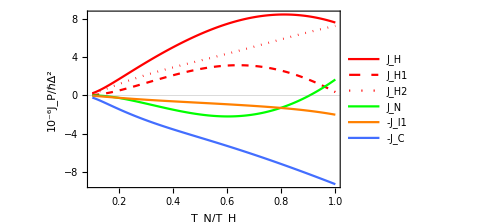
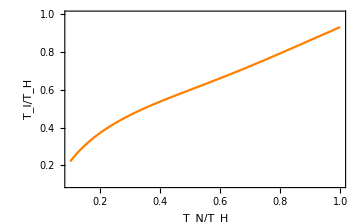
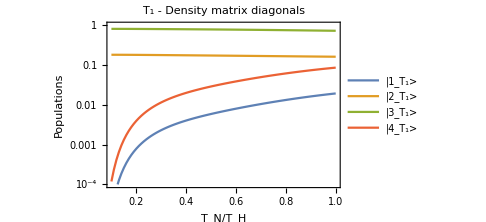
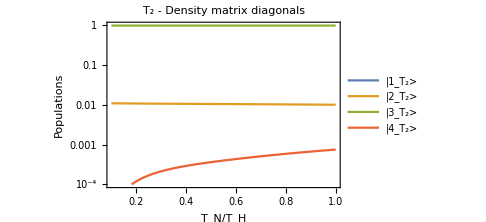
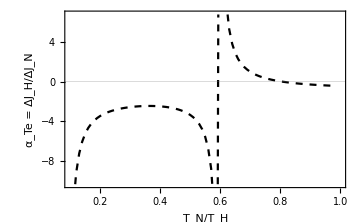

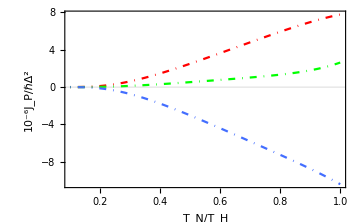

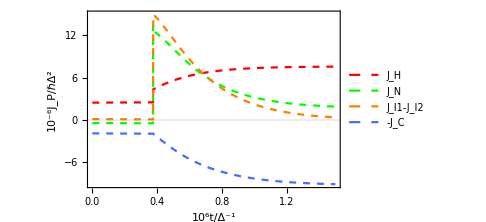
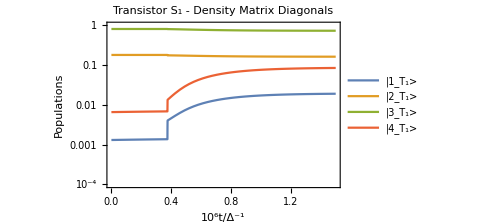

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.3ωconv;ωMR1=0.4ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=0.9ωconv;ωMR=1.1 ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

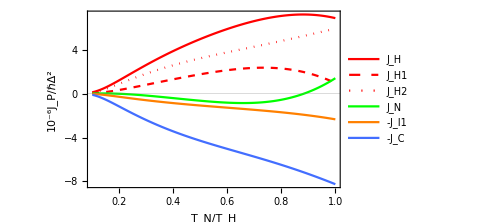
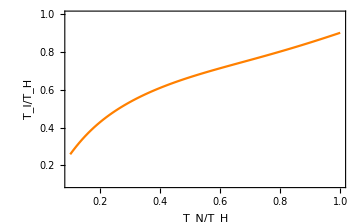
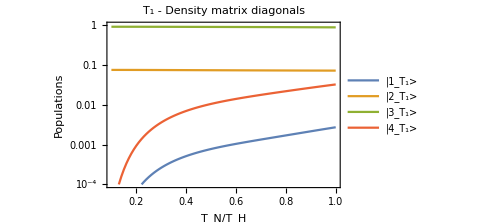
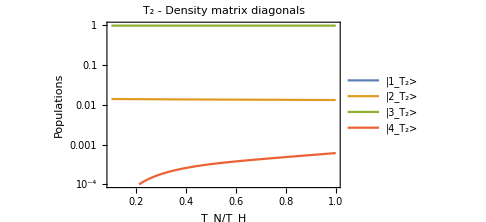
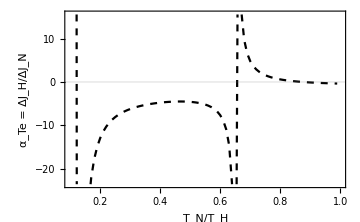

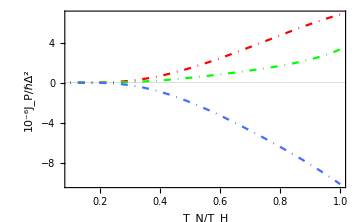

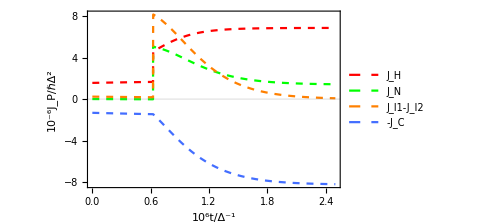
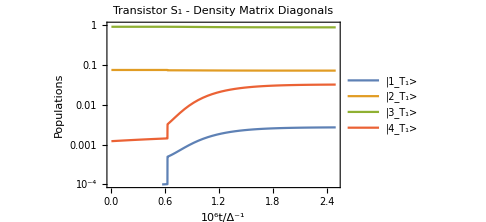

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.85 ωconv;ωMR2=1.15ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=0.85ωconv;ωMR=1.15 ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.85ωconv;ωMR2=1.15 ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=2.5 10^6/ωconv;tchange=0.25 tmax;tstart=-2.5tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

#### To compare with - Energy divider N = 4, p = 3, q = 1 case

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

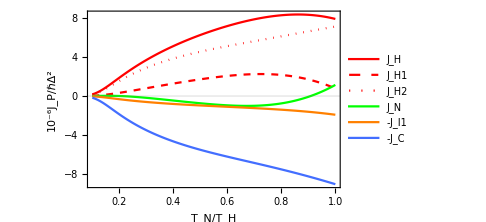
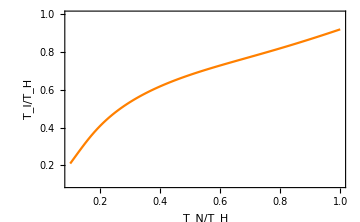
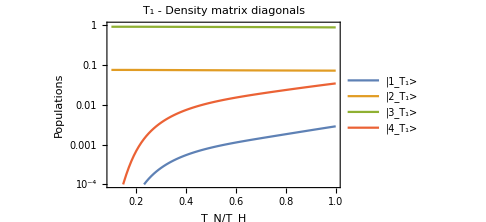
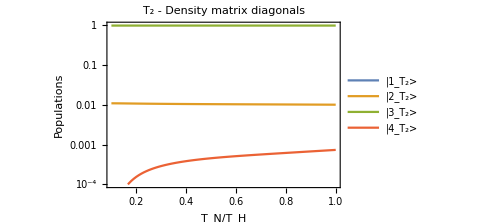
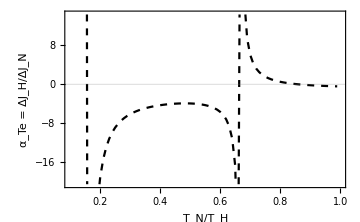

-Graphics-

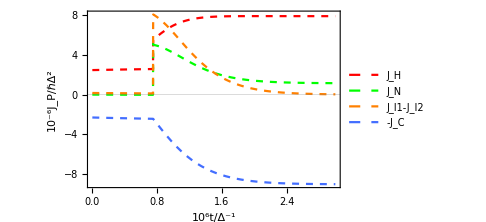
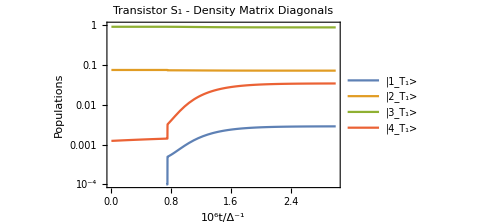
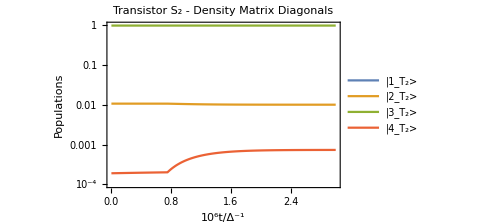
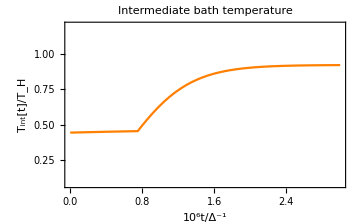

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.9ωconv;ωMR2=1.1ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=0.9ωconv;ωMR=1.1ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.9ωconv;ωMR2=1.1ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=3.0 10^6/ωconv;tchange=0.25 tmax;tstart=-2.4tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

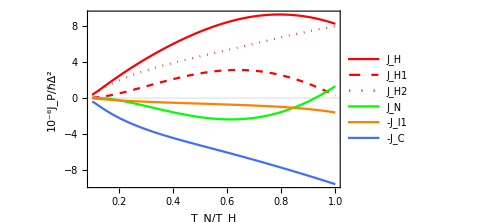
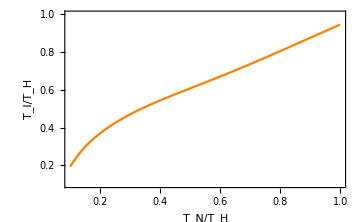
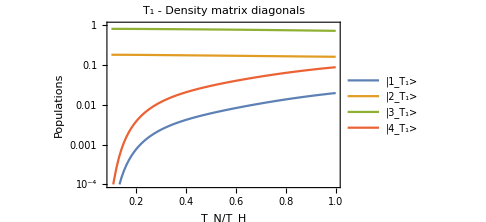
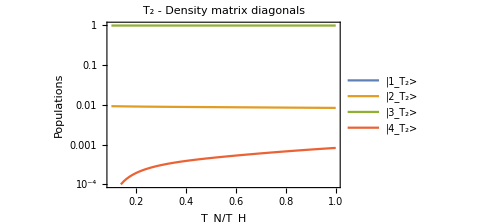
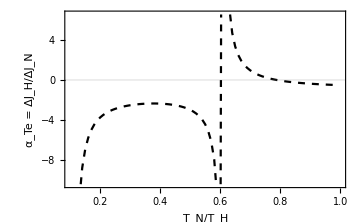

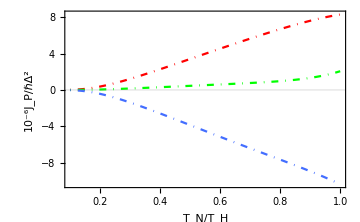

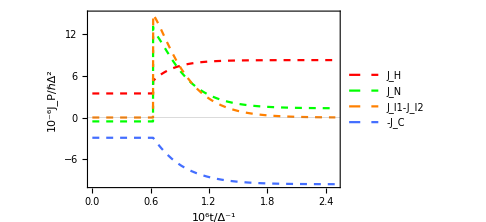
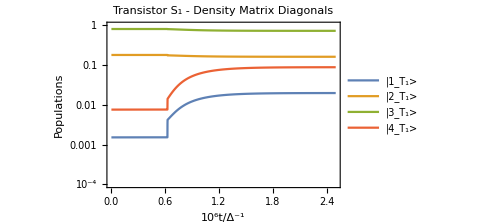

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.3 ωconv;ωMR1=0.4ωconv;
ωLM2=(1.0 - 0.4/6)ωconv;ωMR2=(1.0+ 0.4/6)ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=(1.0 - 0.4/6)ωconv;ωMR=(1.0+ 0.4/6) ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4ωconv;
ωLM2=(1.0 - 0.4/6)ωconv;ωMR2=(1.0+ 0.4/6)ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=2.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

#### To compare with - Energy divider N = 5, p = 3, q = 2 case

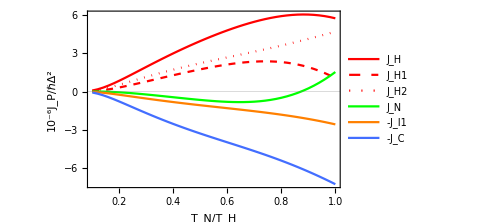
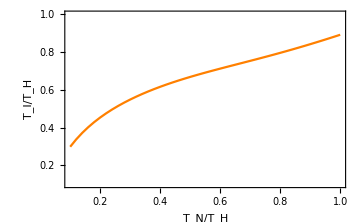
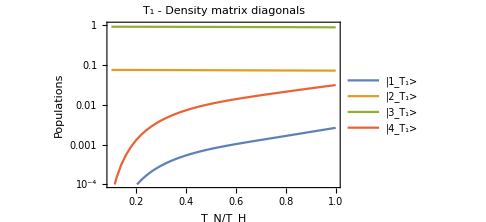
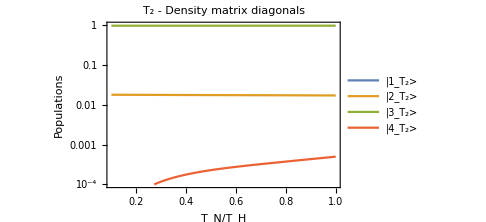
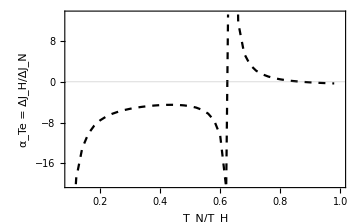

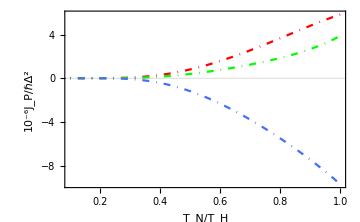

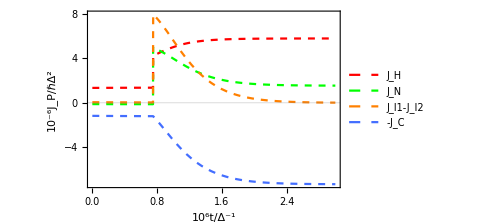
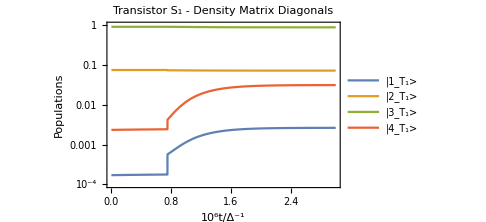

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.8ωconv;ωMR2=1.2ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.004Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=0.8ωconv;ωMR=1.2ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.004Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.8ωconv;ωMR2=1.2ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=3.0 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

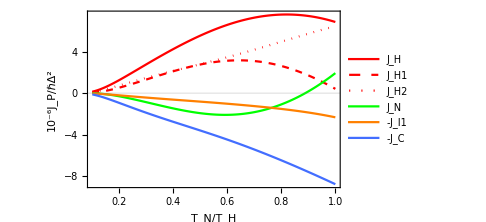
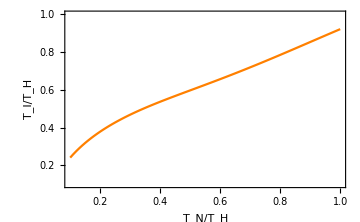
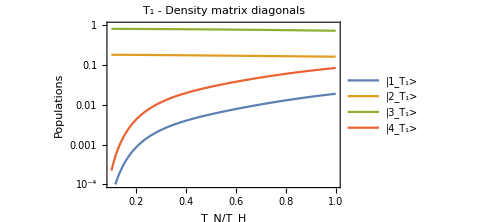
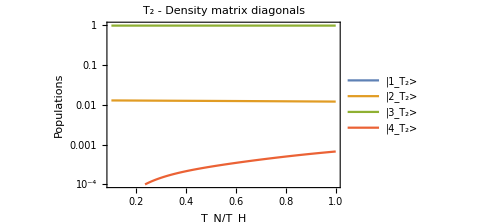
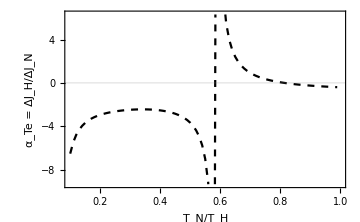

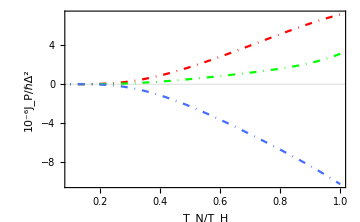

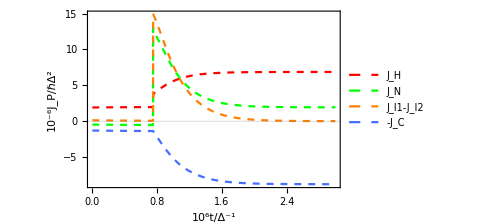
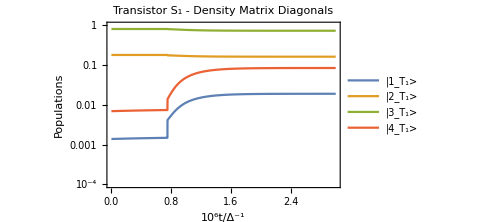

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres},
ωLM1=0.3 ωconv;ωMR1=0.4ωconv;
ωLM2=(1.0 - 2 0.4/6)ωconv;ωMR2=(1.0+2 0.4/6)ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.001;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres},
ωLM=(1.0 - 2 0.4/6)ωconv;ωMR=(1.0+ 2 0.4/6) ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,Tcntmin,Tcntmax,Tres,False]
]
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4ωconv;
ωLM2=(1.0 - 2 0.4/6)ωconv;ωMR2=(1.0+2 0.4/6)ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;κint=0.01;
mCint=50mCconv;
Tcnt1s=0.05Tconv;Tcnt2s=0.2Tconv;
tmax=3.0 10^6/ωconv;tchange=0.25 tmax;tstart=-1.5tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2, Tcnt1s,Tcnt2s,tstart,tchange,tmax]
]
```

## Plots for adjusting Ω while keeping T_CNT constant (operation as an optically controlled thermal gate)

### Absolute thermal flows

Inwards energy flows when temperature Ω is changed, keeping T_CNT constant,

```mathematica
PlotEngyFlowsWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_,Ω1min_,Ω1max_,Ω1res_,legends_]:=Module[{tempx,tempy,denmatT1,denmatT2,inttemps,combflows,amplif},
tempx=Table[{Ω1/(κhot ωconv),Ω1/(κhot ωconv),Ω1/(κhot ωconv),Ω1/(κhot ωconv)},{Ω1,Ω1min,Ω1max,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,Ω1,ωLM2,ωMR2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,1,1,i]]}],{i,1,4}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,2,1,i]]}],{i,1,4}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]/Thot}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],10^6(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])}],
	MapThread[List,{tempx[[;;,1]],10^6 tempy[[;;,2,1,3,1]]}],
	MapThread[List,{tempx[[;;,1]],10^6 tempy[[;;,2,2,3,1]]}],
	MapThread[List,{tempx[[;;,2]],10^6 tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],10^6 tempy[[;;,2,1,3,3]]}],
	MapThread[List,{tempx[[;;,3]],10^6 tempy[[;;,2,2,3,3]]}],
	MapThread[List,{tempx[[;;,4]],10^6 tempy[[;;,2,1,3,4]]}]
};
amplif=MapThread[List,{Drop[tempx[[;;,1]],-1],Differences[(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])]/Differences[tempy[[;;,2,1,3,4]]]}];
{
ListPlot[combflows,
	ImageSize->Medium,
	PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_H1",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_H2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_I1",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red},{Red,Dashed},{Red,Dotted},{Green},{Orange},{BlueC},{PurpleC}},
	Joined->True],
ListPlot[inttemps,
	ImageSize->Medium,
	PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{Tcol/Thot,Thot/Thot+0.2}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["T_I/T_H",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	PlotStyle->{Orange},
	Joined->True],
ListLogPlot[denmatT1,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT2,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListPlot[amplif,
	ImageSize->Medium,
	PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Op = ΔJ_H/ΔJ_F",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Black,Dashed}},
	Joined->True]
}]
```

For comparison, a single temperature-controlled quantum thermal transistor

```mathematica
PlotEngyFlowsWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωLM_,ωMR_,Ωmin_,Ωmax_,Ωres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=Table[{Ω/(κhot ωconv),Ω/(κhot ωconv),Ω/(κhot ωconv),Ω/(κhot ωconv)},{Ω,Ωmin,Ωmax,Ωres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,3,i]]}],{i,1,4}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotRange->{Automatic,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
	PlotStyle->{{Red,DotDashed},{Green,DotDashed},{BlueC,DotDashed},{PurpleC,DotDashed}},
	Joined->True]
]
```

### Time domain behaviors

```mathematica
PlotTimeDomainWithΩ[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κints_,κcols_,mCints_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_, Ωcnt1s_,Ωcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1s,t<tchange},{Ωcnt2s,t>tchange}}]
};
sysassum = {
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->Ω2,
Thot-> Thots,Tcol-> Tcols,Tcnt-> Tcnts,
κhot->κhots,κcol->κcols,κcnt->κcnts,κint->κints,
mCint->mCints
};

motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcols,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,tstart,tmax}
];

tempgraph = (Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
denmatS1graph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.dynamics];
denmatS2graph=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,4}]}/.dynamics];
flowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 t;

indsysassum={
Subscript[ωLM, 1]->ωLM2,Subscript[ωMR, 1]->ωMR2,
Subscript[T, 1,1]-> Thots,Subscript[T, 1,2]-> Tcnts,Subscript[T, 1,3]->Tcols,
Subscript[κ, 1,1]-> κhots,Subscript[κ, 1,2]-> κcnts,Subscript[κ, 1,3]->κcols,
Subscript[Ω, 1]->Ωcnt
};

indmotioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
indinitconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.indsysassum;

inddynamics = NDSolve[
Flatten[{indmotioneqs,indinitconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,tstart,tmax}
];

inddenmatgraph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.inddynamics];
indflowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.inddynamics]/.t->10^6 t;

{{
Plot[tempgraph[10^6 t],{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Intermediate bath temperature",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.5Thot/Thot)/.sysassum},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["T_int[t]/T_H",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Orange}
],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
GridLines->{None,{0}},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
],
timedom=Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Full},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
PlotStyle->{{Red,Dashed},{Green,Dashed},{Orange,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}
]
},
{
LogPlot[inddenmatgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Single transistor - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange->{Automatic,Automatic},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
PlotLegends->{
Style["|1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4>",FontFamily->"Times New Roman",FontSize->14.5]}
],
singtimedom=Plot[indflowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Automatic},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
GridLines->{None,{0}},
PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
}}
]
```

```mathematica
PlotTimeDomainWithΩ[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κints_,κcols_,mCints_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_, Ωcnt1s_,Ωcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1s,t<tchange},{Ωcnt2s,t>tchange}}]
};
sysassum = {
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->Ω2,
Thot-> Thots,Tcol-> Tcols,Tcnt-> Tcnts,
κhot->κhots,κcol->κcols,κcnt->κcnts,κint->κints,
mCint->mCints
};

motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[tstart]==Tcols,Table[Subscript[ρ, S,i,j][tstart]==i,j i,3 1,{S,1,2},{i,1,4},{j,1,4}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,4},{j,1,4}],Tint}],{t,tstart,tmax}
];

tempgraph = (Tint[#]/Thot)/.Flatten[{dynamics,sysassum}] &;
denmatS1graph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.dynamics];
denmatS2graph=Flatten[{Table[Subscript[ρ, 2,i,i][10^6 t],{i,1,4}]}/.dynamics];
flowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]),Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics]/.t->10^6 t;

indsysassum={
Subscript[ωLM, 1]->ωLM2,Subscript[ωMR, 1]->ωMR2,
Subscript[T, 1,1]-> Thots,Subscript[T, 1,2]-> Tcnts,Subscript[T, 1,3]->Tcols,
Subscript[κ, 1,1]-> κhots,Subscript[κ, 1,2]-> κcnts,Subscript[κ, 1,3]->κcols,
Subscript[Ω, 1]->Ωcnt
};

indmotioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
indinitconditions={Table[Subscript[ρ, 1,i,j][tstart]==i,j i,3 1,{i,1,4},{j,1,4}]}/.indsysassum;

inddynamics = NDSolve[
Flatten[{indmotioneqs,indinitconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,4},{j,1,4}]}],{t,tstart,tmax}
];

inddenmatgraph=Flatten[{Table[Subscript[ρ, 1,i,i][10^6 t],{i,1,4}]}/.inddynamics];
indflowgraph=Flatten[10^6{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.inddynamics]/.t->10^6 t;

{
Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic,Full},
Axes->False,
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_I1-J_I2",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
PlotStyle->{{Red,Dashed},{Green,Dashed},{Orange,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}
],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {0.0001,1},
GridLines->{None,{0}},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["Populations",FontFamily->"Times New Roman",FontSize->16]}, 
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
],
Plot[tempgraph[10^6 t],{t,0,10^-6 tmax},
ImageSize->Medium,
PlotLabel->  Style["Intermediate bath temperature",FontFamily->"Times New Roman",FontSize->16],
PlotRange-> {(0.8Tcol/Thot)/.sysassum,(1.5Thot/Thot)/.sysassum},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["T_int[t]/T_H",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Orange}
]
}
]
```

#### To compare with - Energy divider N = 3, p = 2, q = 1 case

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

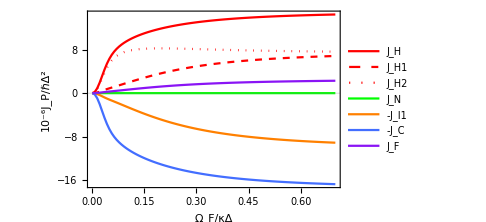
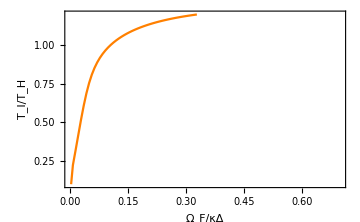
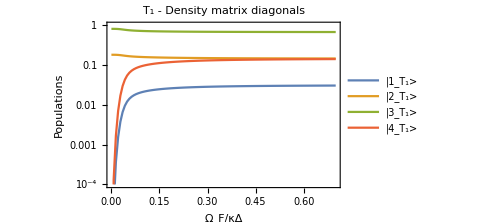
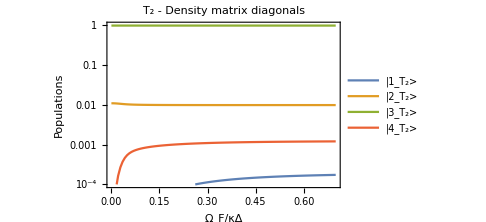
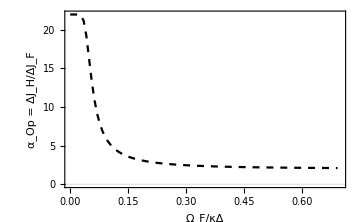

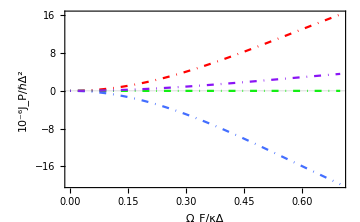

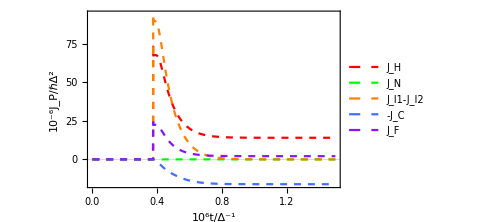
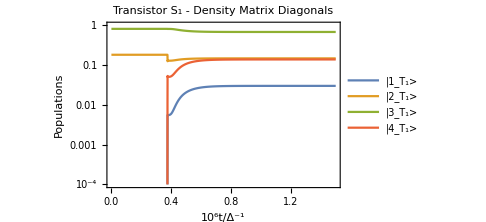

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=0.9ωconv;ωMR=1.1ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

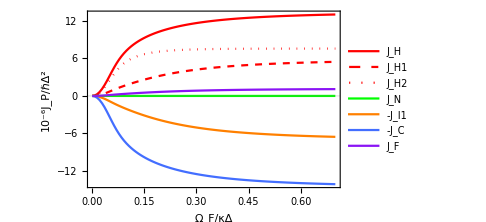
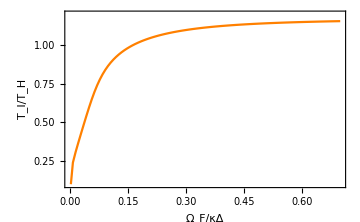
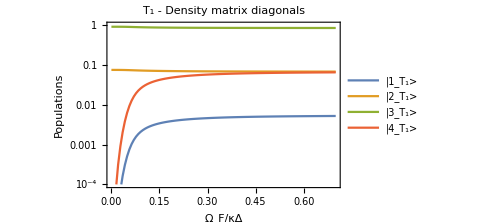
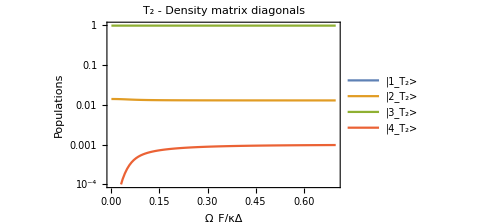
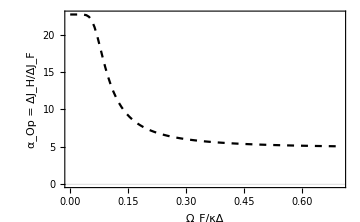

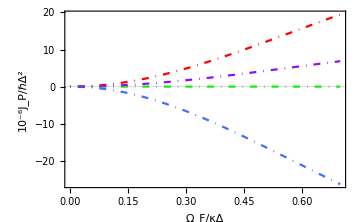

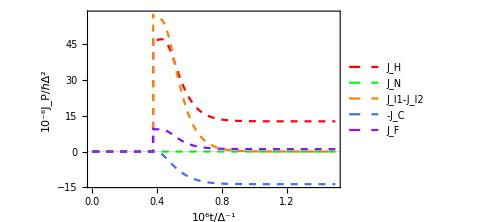
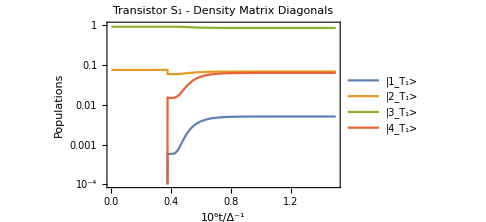

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.85 ωconv;ωMR2=1.15 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=0.85ωconv;ωMR=1.15ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.85 ωconv;ωMR2=1.15 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

#### To compare with - Energy divider N = 4, p = 3, q = 1 case

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

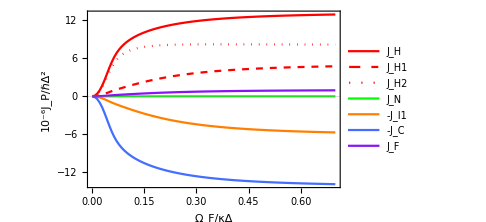
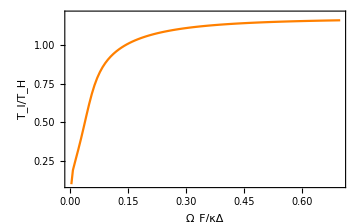
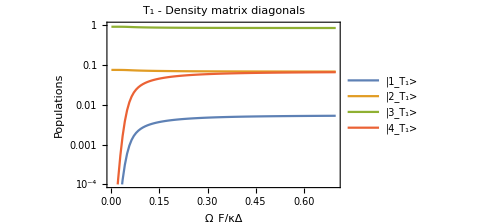
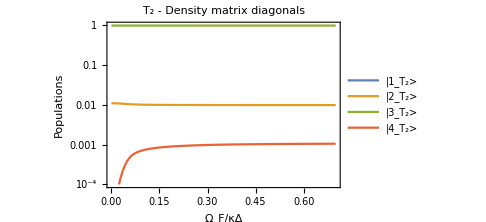
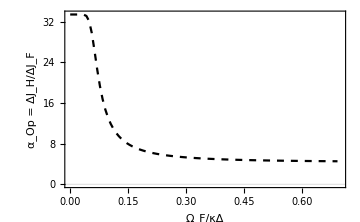

-Graphics-

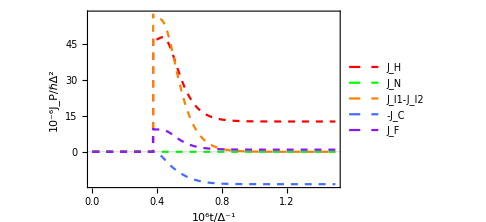
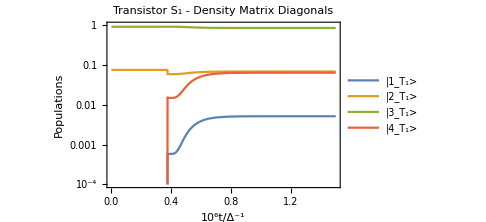
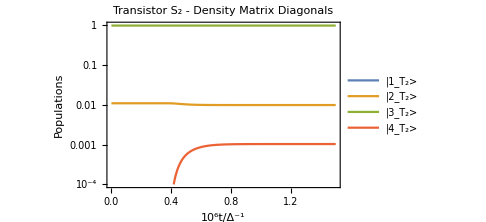
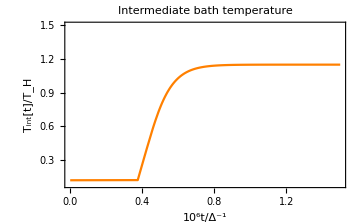

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=0.9ωconv;ωMR=1.1ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

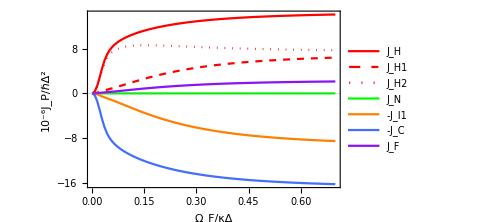
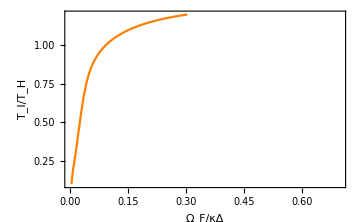
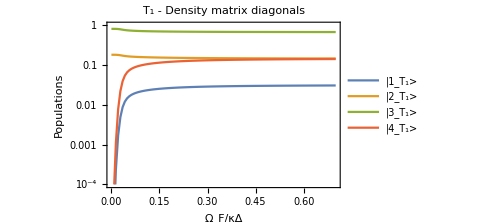
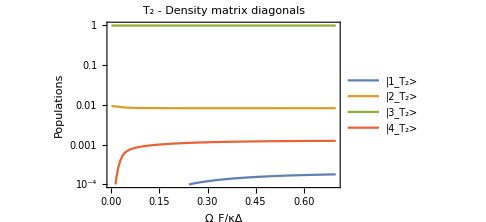
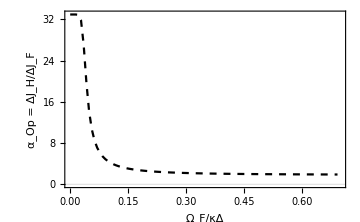

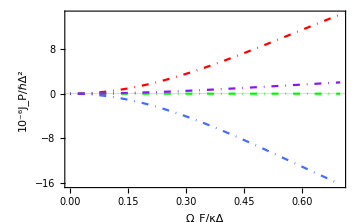

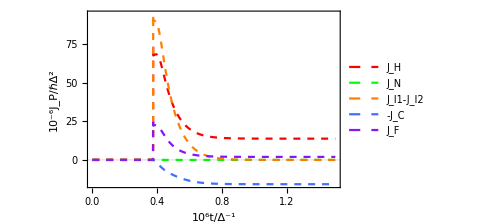
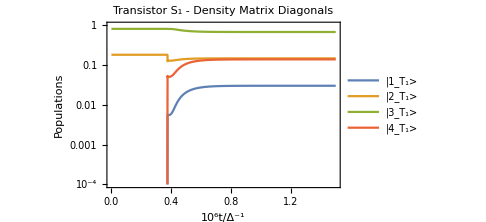

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=(1.0-0.4/6)ωconv;ωMR2=(1.0+ 0.4/6) ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=(1.0- 0.4/6)ωconv;ωMR=(1.0+ 0.4/6)ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=(1.0-0.4/6)ωconv;ωMR2=(1.0+ 0.4/6) ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

#### To compare with - Energy divider N = 5, p = 3, q = 2 case

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

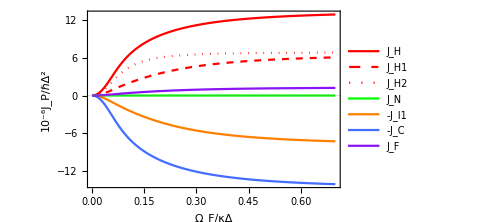
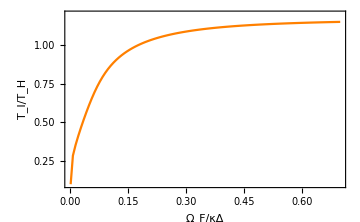
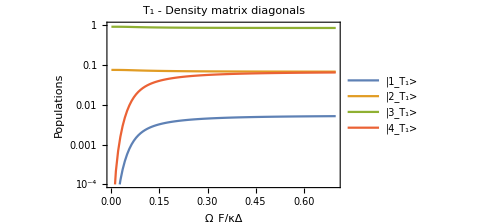
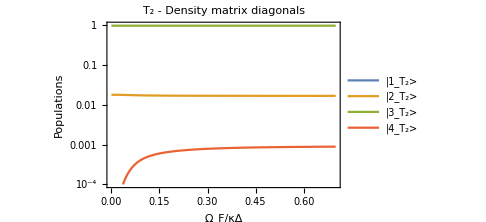
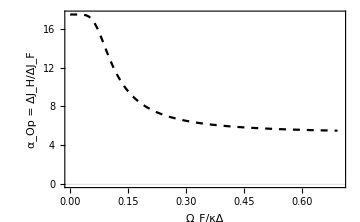

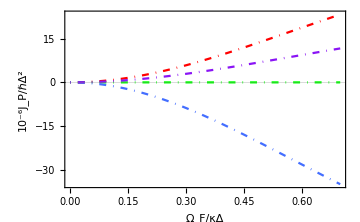

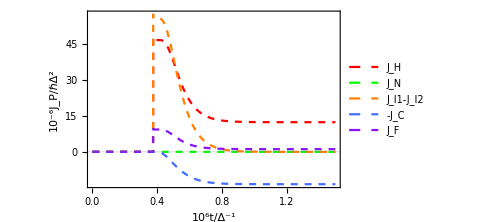
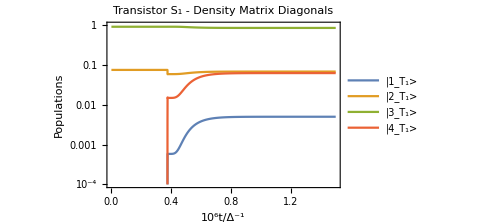

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.8 ωconv;ωMR2=1.2 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=0.8ωconv;ωMR=1.2ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.5 ωconv;ωMR1=0.6 ωconv;
ωLM2=0.8 ωconv;ωMR2=1.2 ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

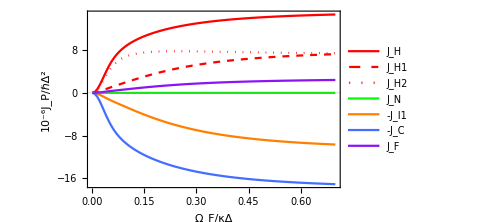
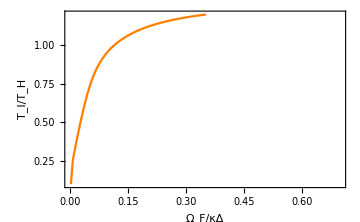
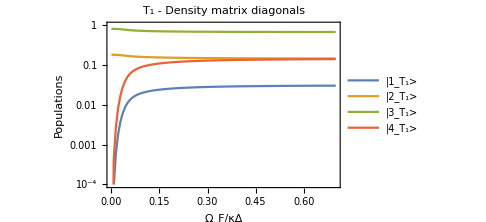
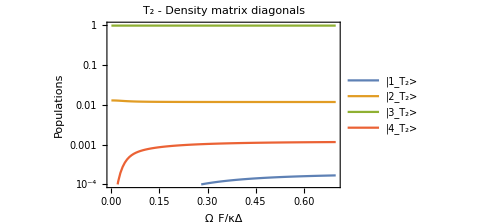
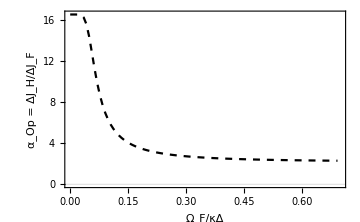

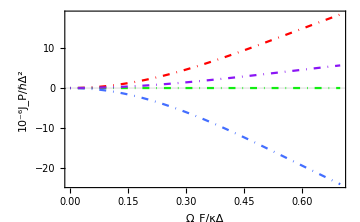

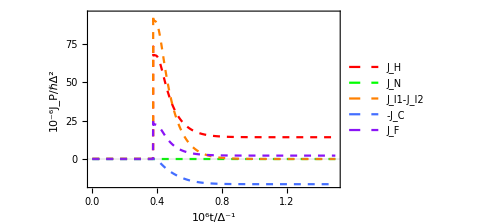
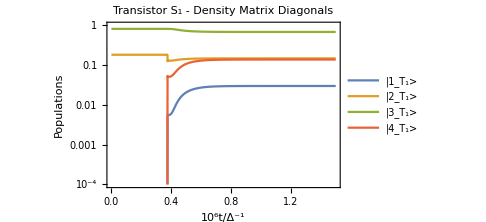

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=(1.0-2 0.4/6)ωconv;ωMR2=(1.0+ 2 0.4/6) ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres},
ωLM=(1.0- 2 0.4/6)ωconv;ωMR=(1.0+ 2 0.4/6)ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM,ωMR,Ωmin,Ωmax,Ωres,False]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint, ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax},
ωLM1=0.3 ωconv;ωMR1=0.4 ωconv;
ωLM2=(1.0-2 0.4/6)ωconv;ωMR2=(1.0+ 2 0.4/6) ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;κint=0.01;
mCint=50mCconv;
Ωcnt1s=0.01ωconv*κhot;Ωcnt2s=0.5ωconv*κhot;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=-3tmax;
PlotTimeDomainWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,mCint,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, Ωcnt1s,Ωcnt2s,tstart,tchange,tmax]
]
```